Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 5. Equazioni differenziali

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 5.1 (Dinamica caotica)

### Testo dell’esercizio

Creare un' animazione del moto di un pendolo doppio.  Prevedere la possibilità di variare il tempo di integrazione e le condizioni iniziali.
Magari mostrare in una seconda finestra gli angoli formati dai due pendoli in funzione del tempo. 

Facoltativo: farlo per un sistema costituito da 3 pendoli. Far generare automaticamente le equazioni di Lagrange a Mathematica.

### Svolgimento

```mathematica
ClearAll["Global *"]
```

Iniziamo implementando le equazioni differenziali: 
per prima cosa diamo delle coordinate ai due punti e deriviamoli

```mathematica
P1[{φ1_,φ2_}]:={Sin[φ1],-Cos[φ1]};
P2[{φ1_,φ2_}]:={Sin[φ2]+Sin[φ1],-Cos[φ2]-Cos[φ1]};
v1[{φ1_,φ2_}]:=D[P1[{φ1[t],φ2[t]}], t];
v2[{φ1_,φ2_}]:=D[P2[{φ1[t],φ2[t]}], t];
normsq[{x_,y_}]:=x^2+y^2
Lform=1/2(normsq[v1[{φ1,φ2}]]+normsq[v2[{φ1,φ2}]])+1/2((φ1'[t])^2+(φ2'[t])^2)-(P1[{φ1[t],φ2[t]}]⟦2⟧+P2[{φ1[t],φ2[t]}]⟦2⟧)//Simplify;
L = 1/2(2 φ1'[t]^2+φ2'[t]^2+2 Cos[φ1[t]-φ2[t]]φ1'[t] φ2'[t] )+(2 Cos[φ1[t]]+ Cos[φ2[t]]) ;
```

ricaviamo le equazioni

```mathematica
eq1 =Simplify[(D[(D[L, φ1'[t]]), t])-D[L, φ1[t]]];
eq2 =Simplify[(D[(D[L, φ2'[t]]), t])-D[L, φ2[t]]];
dsol [T_,{ϕ10_,ϕ20_,dϕ10_,dϕ20_}]:= NDSolve[{eq1==0,eq2==0,φ1[0]==ϕ10,φ2[0]==ϕ20,φ1'[0]==dϕ10,φ2'[0]==dϕ20},{φ1,φ2},{t,0,T}]
```

ora passiamo alla parte grafica:

```mathematica
psup[{ϕ1_,ϕ2_}]:= Graphics[{PointSize[0.03],Green,Point[P1[{ϕ1,ϕ2}]]}];
pinf[{ϕ1_,ϕ2_}]:= Graphics[{PointSize[0.03],Red,Point[P2[{ϕ1,ϕ2}]]}];
line[{ϕ1_,ϕ2_}]:=Graphics[{Thickness[0.01],Black,Line[{{0,0},P1[{ϕ1,ϕ2}],P2[{ϕ1,ϕ2}]}]}];
bipendolo[ϕ12_]:=Show[line[ϕ12],psup[ϕ12],pinf[ϕ12],AspectRatio->Automatic,Axes->False,Frame->False,PlotRange->{{-2,2},{-2,2}},Ticks->None]

animazione[T_,ϕ1_,ϕ2_,v1_,v2_]:=Module[ {sol},
sol= dsol[T,{ϕ1,ϕ2,v1,v2}];
Animate[GraphicsRow[
		{bipendolo[{φ1[t],φ2[t]}/.sol[[1]]],
Plot[Evaluate[{φ1[ξ],φ2[ξ]}/.sol],{ξ,0,t},
PlotStyle->{Green,Red},
PlotRange->{{0,T},Full},
Ticks->{{Automatic},2 Pi Range[-10,5]}]},ImageSize->Large],{t,0,T},
AnimationRate->3
]]

animazione[100,0,0,0,.1]
```

### Facoltativo

```mathematica
P1t[{φ1_,φ2_,φ3_}]:={Sin[φ1],-Cos[φ1]};
P2t[{φ1_,φ2_,φ3_}]:={Sin[φ2]+Sin[φ1],-Cos[φ2]-Cos[φ1]};
P3t[{φ1_,φ2_,φ3_}]:= {Sin[φ2]+Sin[φ1]+Sin[φ3],-Cos[φ1]-Cos[φ2]-Cos[φ3]};
v1t[{φ1_,φ2_,φ3_}]:=D[P1t[{φ1[t],φ2[t],φ3[t]}], t];
v2t[{φ1_,φ2_,φ3_}]:=D[P2t[{φ1[t],φ2[t],φ3[t]}], t];
v3t[{φ1_,φ2_,φ3_}]:=D[P3t[{φ1[t],φ2[t],φ3[t]}], t];
normsq[{x_,y_}]:=x^2+y^2
Lt=1/2(normsq[v1t[{φ1,φ2,φ3}]]+normsq[v2t[{φ1,φ2,φ3}]]+normsq[v3t[{φ1,φ2,φ3}]])+1/2((φ1'[t])^2+(φ2'[t])^2+(φ3'[t])^2)-(P1t[{φ1[t],φ2[t],φ3[t]}]⟦2⟧+P2t[{φ1[t],φ2[t],φ3[t]}]⟦2⟧+P3t[{φ1[t],φ2[t],φ3[t]}]⟦2⟧)//Simplify;
```

```mathematica
eq1t=Simplify[(D[(D[Lt, φ1'[t]]), t])-D[Lt, φ1[t]]];
eq2t =Simplify[(D[(D[Lt, φ2'[t]]), t])-D[Lt, φ2[t]]];
eq3t=Simplify[(D[(D[Lt, φ3'[t]]), t])-D[Lt, φ3[t]]];
solt [T_,{ϕ10_,ϕ20_,ϕ30_,dϕ10_,dϕ20_,dϕ30_}]:= NDSolve[{eq1t==0,eq2t==0,eq3t==0,φ1[0]==ϕ10,φ2[0]==ϕ20,φ1'[0]==dϕ10,φ2'[0]==dϕ20,φ3[0]==ϕ30,φ3'[0]==dϕ30},{φ1,φ2,φ3},{t,0,T}]
```

```mathematica
psupt[{ϕ1_,ϕ2_,ϕ3_}]:= Graphics[{PointSize[0.03],Green,Point[P1t[{ϕ1,ϕ2,ϕ3}]]}];
pmedt[{ϕ1_,ϕ2_,ϕ3_}]:= Graphics[{PointSize[0.03],Red,Point[P2t[{ϕ1,ϕ2,ϕ3}]]}];
pinft[{ϕ1_,ϕ2_,ϕ3_}]:= Graphics[{PointSize[0.03],Blue,Point[P3t[{ϕ1,ϕ2,ϕ3}]]}];
linet[{ϕ1_,ϕ2_,ϕ3_}]:=Graphics[{Thickness[0.01],Black,Line[{{0,0},P1t[{ϕ1,ϕ2,ϕ3}],P2t[{ϕ1,ϕ2,ϕ3}],P3t[{ϕ1,ϕ2,ϕ3}]}]}];
tripendolo[ϕ123_]:=Show[linet[ϕ123],psupt[ϕ123],pmedt[ϕ123],pinft[ϕ123],AspectRatio->Automatic,Axes->False,Frame->False,PlotRange->{{-3,3},{-3,3}},Ticks->None]

animazione[T_,ϕ1_,ϕ2_,ϕ3_,v1_,v2_,v3_]:=Module[ {sol},
sol=solt[T,{ϕ1,ϕ2,ϕ3,v1,v2,v3}];
Animate[GraphicsRow[
		{tripendolo[{φ1[t],φ2[t],φ3[t]}/.sol[[1]]],
Plot[Evaluate[{φ1[ξ],φ2[ξ],φ3[ξ]}/.sol],{ξ,0,t},
PlotStyle->{Green,Red,Blue},
PlotRange->{{0,T},Full},
Ticks->{{Automatic},2 Pi Range[-10,5]}]},ImageSize->Large],{t,0,T},
AnimationRate->3
]]

animazione[100,0,0,0,1,0,.1]
```

## Esercizio 5.2 (Esponenti di Lyapunov)

### Testo dell’esercizio

Determinare numericamente l’esponente di Lyapunov per qualche moto del pendolo doppio. 

- Si può per esempio mostrare in due figure affiancate l’evoluzione dei due angoli (su un qualche intervallo temporale) e l’andamento temporale (anche su un intervallo più lungo) della funzione che approssima l’esponente di Lyapunov.

- Eplorare la dipendenza dal dato inziale. Per esempio, c’è differenza fra moti con energia vicina al minimo dell’eneriga potenziale (moti approssimati da piccole oscillazioni) e con energia vicina o superiore a quella del massimo dell’energia potenziale?

### Svolgimento

Ricaviamo intanto due evoluzioni vicine del bipendolo sfruttando il codice della sezione precedente:

```mathematica
ClearAll["Global *"]
```

```mathematica
P1[{φ1_,φ2_}]:={Sin[φ1],-Cos[φ1]};
P2[{φ1_,φ2_}]:={Sin[φ2]+Sin[φ1],-Cos[φ2]-Cos[φ1]};
v1[{φ1_,φ2_}]:=D[P1[{φ1[t],φ2[t]}], t];
v2[{φ1_,φ2_}]:=D[P2[{φ1[t],φ2[t]}], t];
normsq[{x_,y_}]:=x^2+y^2
(*Lform=1/2(normsq[v1[{φ1,φ2}]]+normsq[v2[{φ1,φ2}]])+1/2((φ1'[t])^2+(φ2'[t])^2)-(P1[{φ1[t],φ2[t]}]⟦2⟧+P2[{φ1[t],φ2[t]}]⟦2⟧)//Simplify;*)
L = 1/2(2 φ1'[t]^2+φ2'[t]^2+2 Cos[φ1[t]-φ2[t]]φ1'[t] φ2'[t] )+(2 Cos[φ1[t]]+ Cos[φ2[t]]) ;
eq1 =Simplify[(D[(D[L, φ1'[t]]), t])-D[L, φ1[t]]];
eq2 =Simplify[(D[(D[L, φ2'[t]]), t])-D[L, φ2[t]]];
dsol [T_,{ϕ10_,ϕ20_,dϕ10_,dϕ20_}]:= NDSolve[{eq1==0,eq2==0,φ1[0]==ϕ10,φ2[0]==ϕ20,φ1'[0]==dϕ10,φ2'[0]==dϕ20},{φ1,φ2},{t,0,T}]

stable1[t]=Evaluate[φ2[t]/.dsol[40,{0,0,0,.1}]];
stable2[t]=Evaluate[φ2[t]/.dsol[40,{0,0,0,.1+10 $MachineEpsilon}]];

unstable1[t]= Evaluate[φ2[t]/.dsol[40,{π,π,0,.1}]];
unstable2[t]=Evaluate[φ2[t]/.dsol[40,{π,π,0,.1+10 $MachineEpsilon}]];
```

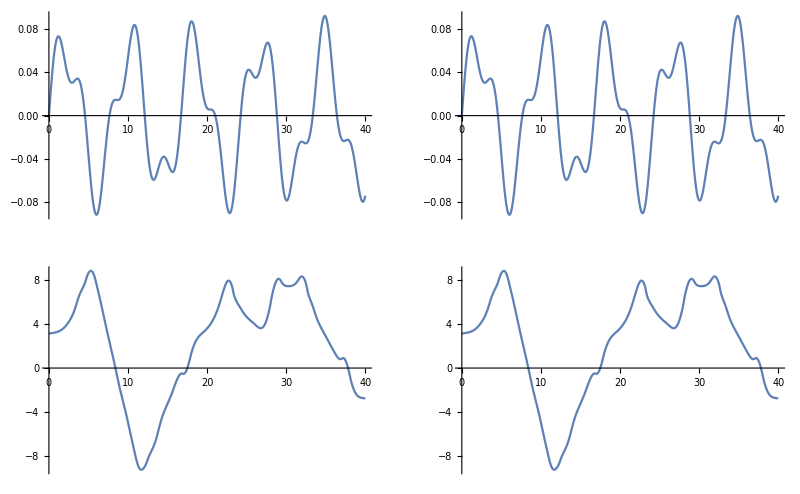

```mathematica
GraphicsGrid[Partition[Plot[#,{t,0,40}]&/@{stable1[t],stable2[t],unstable1[t],unstable2[t]},2]]
```

a occhio nudo sono identiche, tuttavia se guardiamo (il logaritmo) della differenza tra le orbite

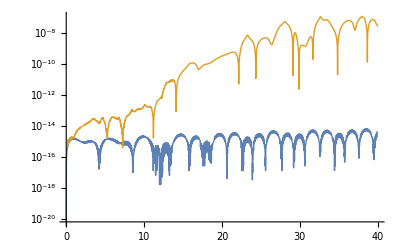

```mathematica
LogPlot[{RealAbs[stable1[t]-stable2[t]],RealAbs[unstable1[t]-unstable2[t]]},{t,0,40},PlotStyle->Thick,ImageSize->Full]
```

Vi è una separazione tra le orbite instabili (arancione) più che nelle orbite stabili (blu)

Per calcolare l’esponente di Lyapunov serve controllare l’evoluzione della derivata delle funzioni lungo un’orbita

```mathematica
right0=Solve[{eq1,eq2}=={0,0}, {φ1''[t],φ2''[t]}]//FullSimplify;
right1= {φ1''[t],φ2''[t]}/.right0;
right=right1/.{φ1[t]->φ1,φ2[t]->φ2,φ1'[t]->ω1,φ2'[t]->ω2};
X[{φ1_,φ2_,ω1_,ω2_}]=Join[{ω1,ω2},right];
JX=D[X[{φ1,φ2,ω1,ω2}],{{φ1,φ2,ω1,ω2}}];
Y[{z_,u_}]:={X[z],JX[z].u}
```

Implementiamo un algoritmo di tipo “Runge-Kutta”

```mathematica
rk[h_][zu_]:=zu+h Y[zu+h/2 Y[zu]]
orbite[zu_,h_,T_]:= NestList[rk[h],zu,Floor[T/h]]
norme[zu_,h_,T_]:=Norm/@(Transpose[orbite[zu,h,T]]⟦2⟧)
```

```mathematica
orbitainstabile=orbite[ {{Pi,Pi,.01,.1},{1,0,0,1}},.01, 20];
```

Thread::tdlen: Objects of unequal length in {π,π,0.01,0.1}+{0.00005,0.0005,{0.,0.}} cannot be combined.

Thread::tdlen: Objects of unequal length in {π+0.01 X[{0.00005,0.0005,{«2»}}+{π,π,0.01,0.1}],π+0.01 X[{0.00005,0.0005,{«2»}}+{π,π,0.01,0.1}],0.01+0.01 X[{0.00005,0.0005,{«2»}}+{π,π,0.01,0.1}],0.1+0.01 X[{0.00005,0.0005,{«2»}}+{π,π,0.01,0.1}]}+{0.005 (0.01+0.01 X[{«3»}+{«4»}]),0.005 (0.1+0.01 X[{«3»}+{«4»}]),{-0.0025 (0.+Sin[Times[«2»]+Times[«2»]]-3 Sin[Times[«2»]]),0.}} cannot be combined.

Thread::tdlen: Objects of unequal length in {π+0.01 X[{0.00005,0.0005,{«2»}}+{π,π,0.01,0.1}]+0.01 X[{Times[«2»],Times[«2»],{«2»}}+{Plus[«2»],Plus[«2»],Plus[«2»],Plus[«2»]}],π+0.01 X[{0.00005,0.0005,{«2»}}+{π,π,0.01,0.1}]+0.01 X[{Times[«2»],Times[«2»],{«2»}}+{Plus[«2»],Plus[«2»],Plus[«2»],Plus[«2»]}],0.01+«1»+0.01 X[{«1»}+{«1»}],0.1+0.01 X[{0.00005,0.0005,{«2»}}+{π,π,0.01,0.1}]+0.01 X[{Times[«2»],Times[«2»],{«2»}}+{Plus[«2»],Plus[«2»],Plus[«2»],Plus[«2»]}]}+«1» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.